URL[https://mc-stan.org/learn-stan/case-studies/model-based_causal_inference_for_RCT.html]

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
<<"sampler`";
<<"bugs`";
<<"diagnostics`";
n=500;
α=1;
τ=0.25;
nt=200;
w=RandomSample[Join[Table[0,n-nt],Table[1,nt]]];
μc=α+0τ;
σc=1;
μt=α+1τ;
σt=1;
ρ=0.;
Σ={{σc^2,ρ σc σt},{ρ σc σt,σt^2}};
science=RandomVariate[MultinormalDistribution[{μc,μt},Σ],n];
y0=science[[;;,1]];
y1=science[[;;,2]];
yobs=y0(1-w)+y1 w;
U[alpha_,tau_,sigmat_,sigmac_]=Simplify[dnorm[alpha,0,1/25]+dnorm[tau,0,1/25]+dnorm[sigmac,0,1/25]+dnorm[sigmat,0,1/25]+Sum[dnorm[yobs[[i]],alpha+tau w[[i]],1/(sigmat w[[i]]+sigmac(1-w[[i]]))^2],{i,n}]];
Uq[a_,b_,c_,d_]=N[D1[U[a,b,c,d],{a,b,c,d}]];
Uqq[a_,b_,c_,d_]=N[D2[U[a,b,c,d],{a,b,c,d}]];
```

```mathematica
Dim=4;
BURNIN=5000;
ITERATIONS=6000;
PARTICLES=3;
INTERVAL=1001;
STEPS=3;
outbnd[q_]:=q[[3]]<=0||q[[4]]<=0;
qinit=RandomVariate[UniformDistribution[],{PARTICLES,Dim}];
QS=hmc[U,Uq,Uqq,Dim,BURNIN,ITERATIONS,PARTICLES,.5,qinit];
```

10012163.492.16471×10^72.38139×10^70.00003179450.9506640.0854522{2,3}{1,4}False

20022166.993.97051×10^113.97051×10^112.23837×10^-70.5536790.0979141{1}{4}False

30032163.81.06626×10^161.06626×10^161.73343×10^-90.7150270.406137{1,2}{4}False

40042165.166.23157×10^196.23157×10^191.78672×10^-110.6598980.401342{1,2}{4}False

50052167.1.25729×10^241.25729×10^241.67423×10^-130.7700520.398281{1,2}{4}False

```mathematica
psrf[QS,PARTICLES]
```

{1.00774,1.00442,1.05238,1.01803}

```mathematica
Mean[QS]
```

{0.984901,0.276062,0.95088,1.03692}

```mathematica
StandardDeviation[QS]
```

{0.0548595,0.0831159,0.041878,0.0418512}

```mathematica
Quantile[QS,{.1,.5,.9}]//MatrixForm
```

(0.915887 | 0.982948 | 1.05469
0.168653 | 0.278309 | 0.378304
0.895691 | 0.95028 | 1.00525
0.983186 | 1.03802 | 1.09012)

```mathematica
y0=ConstantArray[0,n];
y1=ConstantArray[0,n];
tauUnit=ConstantArray[0,n];
tauFs=ConstantArray[0,Length[QS]];
For[j=1,j<=Length[QS],j++,
For[i=1,i<=n,i++,
alpha=QS[[j,1]];
tau=QS[[j,2]];
sigmat=QS[[j,3]];
sigmac=QS[[j,4]];
muc=alpha;
mut=alpha+tau;
If[w[[i]]==1,y0[[i]]=RandomVariate[NormalDistribution[muc+ρ sigmac/sigmat(yobs[[i]]-mut),sigmac √(1-ρ^2)]];y1[[i]]=yobs[[i]],y1[[i]]=RandomVariate[NormalDistribution[mut+ρ sigmat/sigmac(yobs[[i]]-muc),sigmat √(1-ρ^2)]];y0[[i]]=yobs[[i]]];
tauUnit[[i]]=y1[[i]]-y0[[i]]];
tauFs[[j]]=Mean[tauUnit];
If[Mod[j,100]==0,Print[j]]]
```

100

200

300

400

500

600

700

800

900

1000

1100

1200

1300

1400

1500

1600

1700

1800

1900

2000

2100

2200

2300

2400

2500

2600

2700

2800

2900

3000

```mathematica
Quantile[tauFs,{.1,.5,.9}]
```

```mathematica
{0.19592823735968853,0.2743799385826631,}
```

```mathematica
Mean[tauFs]
```

0.273804

```mathematica
StandardDeviation[tauFs]
```

0.0612178

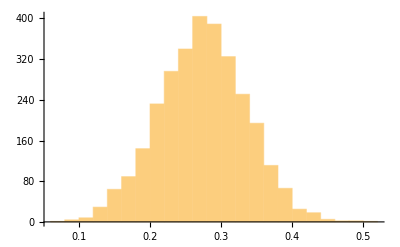

```mathematica
Histogram[tauFs]
```

```mathematica
Mean[tauFs]
```

0.273804

```mathematica
ListPointPlot3D[QS[[;;,1;;3]]]
```

-Graphics3D-

#### computing generated quantities

```mathematica
Collect[{y0-μc,y1-μt}.(Inverse[{{σc^2,ρ σc σt},{ρ σc σt,σt^2}}].{y0-μc,y1-μt}),y0]
```

Dot::dotsh: 张量 {{-0.316278,-0.689565,-0.0819962,1.48357,0.389136,-0.302531,-0.979042,-0.62029,-0.311436,1.74785,«490»},{-1.79165,-0.367494,0.684628,0.331113,0.157928,-0.529963,-0.0675714,0.108583,-0.649224,0.517727,«490»}} 和 {{-0.316278,-0.689565,-0.0819962,1.48357,0.389136,-0.302531,-0.979042,-0.62029,-0.311436,1.74785,«490»},{-1.79165,-0.367494,0.684628,0.331113,0.157928,-0.529963,-0.0675714,0.108583,-0.649224,0.517727,«490»}} 含有不兼容形状.

{{-0.316278,-0.689565,-0.0819962,1.48357,0.389136,-0.302531,-0.979042,-0.62029,-0.311436,1.74785,0.0465755,0.573552,0.0807835,0.052286,0.376254,0.336733,-0.52736,0.411861,-0.0357556,0.920026,0.261762,-0.0311025,2.12381,0.936904,-1.97147,-0.660624,-1.16543,0.533249,0.121548,-1.53501,-0.0544873,0.376961,-0.782241,0.517982,-0.458544,0.0829213,0.874034,1.95179,0.860902,-0.386328,-0.554968,0.443124,-0.411342,1.48629,-0.634265,-1.42526,0.410539,-1.5402,-0.651676,-1.01235,-0.51387,-0.249243,-1.29376,0.0444466,-0.28139,1.25312,-2.82473,1.76612,0.203613,1.13132,0.410255,-0.34278,1.29796,-1.84381,-0.309376,-0.306078,-1.60178,1.53097,0.383659,-0.00806288,-0.379789,0.196653,0.987125,-0.212654,1.60482,1.55503,1.44611,0.0390234,-0.387398,-0.112932,-0.295703,0.760633,-0.84331,0.991296,1.81457,0.906464,-1.82363,-0.960163,-0.728189,1.02897,-0.518526,1.26308,-0.570245,-1.10499,-0.375696,0.513818,-0.185162,-0.374109,0.904418,1.13742,0.428154,-0.481872,-0.616189,-1.81688,-1.11592,0.586533,1.33569,-0.254734,0.73116,-0.20394,1.79105,-1.29607,0.338179,-2.08408,-1.45389,1.1521,0.943855,-0.667418,1.49611,1.17477,1.06937,0.128958,0.054458,0.625084,0.202418,-0.542496,-1.3975,0.708502,-1.46854,0.0811967,-2.68568,-0.0192742,-1.21599,1.20833,0.144339,-1.04866,2.01601,1.31276,-0.289442,0.533415,0.272281,0.890364,-0.0743497,0.533411,-0.10449,-1.08097,-0.0100656,-0.491134,0.679448,-0.707867,1.06321,1.63585,-0.215795,-1.15792,0.631043,-1.29874,0.463225,-0.0840445,-1.03428,-0.023963,0.465618,1.84331,-1.01911,-0.832592,-0.948696,0.677925,-1.68494,-1.40733,0.438458,2.85328,-1.83561,-0.119759,-0.974426,-1.13457,-0.878088,1.64513,0.824671,-0.283868,2.07926,-0.0575524,-0.453699,0.95218,0.668256,0.477916,-0.56599,-0.0506457,-0.824472,0.11745,0.284998,1.57441,-0.411333,-1.63152,-0.488042,2.27978,0.726112,-0.936439,-0.696348,2.37012,-0.92076,0.0364655,0.0457205,0.215104,0.265877,-0.964565,0.659491,2.05534,-0.421816,0.809583,-0.121292,1.86549,-1.11159,-0.163937,-0.478041,0.0738052,0.421601,0.569907,-1.08975,0.135367,-1.32862,0.491918,0.40288,-0.0477535,-0.50794,-0.21144,0.855248,1.64442,-0.559071,1.43576,0.0946533,-0.740062,-1.72346,-1.0887,1.20483,0.258307,0.832468,-1.1066,-1.37226,-1.05104,1.98467,-1.33316,-1.17157,2.46079,1.47974,-1.26506,-0.555111,-1.16018,0.153924,1.51468,-0.085593,-2.69358,1.59265,-0.241808,-0.450651,0.604471,-0.960998,-1.77489,-0.339588,1.40769,-1.68278,0.832111,0.477374,-1.0356,0.292395,2.1472,-0.531374,-1.09013,-0.416735,0.0562909,0.496151,0.506032,-0.973039,1.17533,0.697718,-2.14896,0.185458,-0.75899,-1.91896,1.23696,0.110224,-1.85089,-0.582469,0.297892,-0.844362,1.58192,0.849992,2.74633,-1.16898,-1.35312,-2.52728,0.10485,-1.03001,0.218642,1.92641,-2.15842,0.188136,1.30217,-0.996075,-0.813853,1.39116,1.78678,2.72215,-0.637499,0.218152,0.735004,-1.34987,0.785441,-0.416381,0.194757,-0.703631,-0.064333,-1.22189,2.36351,-0.810425,0.508592,1.10719,-0.829485,0.449283,-1.03766,-0.254645,-1.20322,1.90793,0.320356,-0.528076,1.13913,-0.855282,-0.222083,-1.31556,-0.452947,-0.30004,-0.242005,-0.137782,-0.899754,-0.106786,-0.263068,2.89717,1.28914,-0.00572922,-0.647235,0.42764,-0.199302,-0.349157,3.0957,-0.299833,-1.4493,1.02849,1.26594,0.845821,0.816318,-1.30587,0.802549,1.35321,0.167924,1.00324,0.655965,-0.445518,-0.108431,0.284606,-0.923122,-0.589903,-1.50563,0.548268,-0.36464,-1.27899,-0.617221,1.13176,-1.84348,-0.632475,-0.334655,0.799329,0.777828,-0.673453,-1.51436,0.0264144,1.10809,-0.834384,-1.93788,-0.187791,1.20904,-1.71327,-1.10477,-0.528293,-1.62256,-1.17914,-0.437394,0.0783729,1.88383,2.2019,-1.06587,-0.810896,1.01906,1.23558,-0.871857,-1.85635,1.57574,0.485975,1.27736,0.16836,-0.0753209,-0.0225568,1.23546,-0.221021,0.131853,1.35003,-1.02466,-0.417865,1.10603,-0.266745,-0.721497,0.0924497,0.32996,0.0558579,-0.40425,1.6193,-0.947134,-0.472663,-0.337667,0.299426,-0.548315,-0.958698,2.09389,-2.03061,0.457706,-0.402286,1.16329,0.169416,-1.08348,-1.34574,-1.13288,-0.175215,1.04763,-1.57631,0.37867,-0.465237,-1.21559,-0.825633,0.719849,-0.489168,0.763243,-0.468938,0.692486,1.30804,0.0620617,1.50515,-0.400705,-1.90998,-0.320803,0.0692215,-2.18892,0.942564,-0.160846,-1.75925,-0.266288,0.107391,-0.505092,-0.0275609,-0.0474325,0.616974,-0.329317,-0.0325057,0.788436,1.01411,-2.14137,0.671765,-0.434249,-0.844195,0.411298,-1.11268,0.838245,-1.04436,-0.263191,-1.55057,0.466169,-1.66258,0.219533,0.683465,1.62666,1.22321,-0.908522,0.575739,0.303703,-0.220905,-1.61365,0.212621,0.90954,-0.643958,-1.31451,0.917918,0.373256,-0.894861,1.5921,0.0818522,1.40544,1.57057,1.21764,0.57962,0.387885,0.678304,-0.647041,-0.39909,-0.220421},{-1.79165,-0.367494,0.684628,0.331113,0.157928,-0.529963,-0.0675714,0.108583,-0.649224,0.517727,-0.0804367,0.794632,1.81096,0.0991251,-0.137674,1.05638,-2.53175,-1.89346,1.01193,1.19751,1.03317,1.44791,-0.250028,-0.118882,-0.807351,-0.438174,-0.818301,0.664175,-1.33649,-0.334676,-1.97369,0.055198,0.841618,-1.64848,1.29599,0.193105,2.335,-0.121763,-0.381484,0.868861,0.41985,0.604788,-0.887599,-0.223868,1.437,0.848068,0.297579,-1.38943,-0.133705,-0.329646,0.67898,0.353079,1.2048,-0.0780389,-0.37433,1.35295,-0.36282,0.2756,0.500426,-0.40788,-0.913189,1.55493,-0.139876,0.190954,-0.584231,0.00377962,-1.86534,0.04866,-0.739068,-0.459248,1.91565,1.5225,1.01057,-0.0234794,-1.14637,-1.93363,0.505895,2.32593,0.342806,-0.0819245,0.699878,-1.17582,0.431255,-0.690248,0.364159,-1.8497,0.25773,0.754637,1.25627,0.94594,-0.00428182,-0.0362493,-0.195654,-0.760374,2.16073,-0.143082,0.252978,-0.315007,-0.95497,2.33748,-0.129388,0.791045,-0.120347,0.612708,0.244175,0.0868541,-0.277517,1.05621,1.28634,0.437374,0.844684,0.735774,-0.955049,0.617396,0.336768,0.0175697,-0.507442,-0.634752,-0.465816,1.44884,0.27787,-1.27269,-0.658121,-0.914698,0.898707,-0.870843,-1.22119,-0.0147515,0.0817162,1.13612,-1.27222,0.273416,-0.666601,-0.906589,-0.661526,-0.720645,-0.919669,-1.26856,-0.339455,-0.0470376,0.177529,-0.606957,1.20267,-0.848417,-0.286066,0.495284,0.257716,-0.758115,-0.648822,-1.49314,0.928149,-2.06688,1.12575,0.691534,-0.145066,-0.843605,-0.556563,0.497116,-0.668678,-1.49407,-0.0295237,0.504717,-0.515077,0.941929,1.22727,2.06425,-0.78554,-0.440785,0.892489,-0.861251,0.618393,1.92995,1.14092,-0.171119,0.921335,-0.795111,0.91671,-1.63793,-0.0909642,0.344278,-0.554819,-0.709259,0.546936,-1.06957,0.582651,-0.0663477,0.0891929,1.12846,1.42912,-0.388956,-0.836525,0.54803,-0.741985,-0.505398,1.48207,0.539859,-0.331922,-0.176152,-0.383887,-0.69275,0.72786,-0.452786,0.109176,-0.269642,0.933435,-0.443725,-1.17037,0.345022,-0.35041,-0.363134,0.805063,-0.285286,1.71916,-0.234838,-1.21008,-0.662195,-0.601471,-0.946972,-0.211674,0.319414,-0.65701,-1.18998,-1.97856,-0.0174899,-0.406378,-0.199839,-0.913167,-0.821072,-0.351131,0.121111,-0.905031,1.42284,-0.800912,-1.61251,-0.0607103,-1.40725,0.66548,0.742094,0.634067,0.0335575,-0.461805,1.12989,-0.0303489,-0.570438,0.434594,0.812706,0.441453,-0.00293367,-0.856465,1.1013,-0.483712,-0.201878,1.62974,0.279709,-1.1267,0.922399,-0.668259,-0.685565,0.935367,0.697456,-1.02429,-1.9004,2.17194,-0.311948,-0.920489,-1.38964,-0.0416588,0.573706,0.470082,-0.798665,-1.69362,-0.715451,-0.833289,0.634865,-0.194318,0.318815,-0.746212,0.294488,-1.45682,-0.974919,1.30973,-0.500874,0.352004,0.104219,0.539723,1.4316,-1.10126,0.661232,-0.436935,-1.23544,0.924214,1.11688,1.17359,-1.06746,-0.489713,-0.310783,-2.51519,1.29885,0.663504,1.46637,0.170808,-0.362114,0.382151,0.387897,-0.363378,-1.02569,0.956762,0.828284,-0.823622,0.846584,0.633667,-0.192749,1.02851,-1.46202,0.92071,0.471423,1.08381,-0.470815,0.30376,-0.2028,-0.374767,0.893748,-0.513598,0.404733,-0.971355,-0.979379,-0.855932,0.552007,1.2147,1.54839,-0.295841,-1.03673,-1.14312,0.175565,1.49843,-0.0945846,-0.855226,-0.698901,0.808285,-1.13134,-1.98061,0.254199,1.07742,0.596656,-1.61768,-0.546847,0.35265,-1.76074,-0.227033,-0.298545,-3.00065,0.58937,-0.341293,0.196562,-0.882704,-0.387728,-1.4107,0.885598,2.13794,-0.480637,-1.28674,-0.84937,0.807095,-0.442743,0.177284,-0.781916,-1.44717,1.53254,-0.418586,1.06931,1.42721,-0.47851,-0.41365,-0.724001,-0.910845,1.3229,-0.547471,-0.561312,0.0703889,-2.53519,0.00800897,0.222971,0.548062,-0.0521583,1.83284,0.167234,1.51953,-0.380344,1.72659,1.23903,0.762693,1.0245,1.43207,-0.738086,-0.956145,-1.10006,-0.681143,-1.01747,0.965256,-0.434193,0.345028,0.585933,0.526537,-1.87989,2.10116,-0.147493,-0.582572,1.20191,-1.09563,-2.03408,-0.331326,0.64332,-0.963072,-0.599654,-0.111478,-0.322376,0.0152179,1.5753,-1.3532,-0.831822,-1.01207,1.26893,-0.130222,0.507307,0.718332,0.189414,1.71545,-1.158,0.958801,1.26932,-0.309688,0.33487,-1.41083,0.64541,-1.30364,-0.611712,0.0120406,-0.513133,1.06653,0.563518,0.470769,1.24285,1.52844,0.835722,0.165906,-0.0688165,0.163681,1.53196,0.546832,-0.391285,0.645246,-0.56287,-3.2032,0.160576,-1.24108,-0.164703,-1.10057,-0.540545,-0.153705,-0.11226,-0.729655,-0.658401,-0.345882,1.06125,-0.778965,-0.151788,0.60382,-0.430125,1.72071,-0.873893,0.0157025,-0.115291,-0.400175,-1.46859,0.743886,1.25334,0.68106,0.218325,-0.38996,1.17404,0.328991,-1.21714,-0.363386,-1.52987,-0.532028,0.199318,1.28771,-0.353929,1.97917,1.02947,-0.0233242,0.756059,-0.522605,-0.378926,0.809509,-0.417264,0.848825,0.818707,-0.42052,0.536989}}.{{-0.316278,-0.689565,-0.0819962,1.48357,0.389136,-0.302531,-0.979042,-0.62029,-0.311436,1.74785,0.0465755,0.573552,0.0807835,0.052286,0.376254,0.336733,-0.52736,0.411861,-0.0357556,0.920026,0.261762,-0.0311025,2.12381,0.936904,-1.97147,-0.660624,-1.16543,0.533249,0.121548,-1.53501,-0.0544873,0.376961,-0.782241,0.517982,-0.458544,0.0829213,0.874034,1.95179,0.860902,-0.386328,-0.554968,0.443124,-0.411342,1.48629,-0.634265,-1.42526,0.410539,-1.5402,-0.651676,-1.01235,-0.51387,-0.249243,-1.29376,0.0444466,-0.28139,1.25312,-2.82473,1.76612,0.203613,1.13132,0.410255,-0.34278,1.29796,-1.84381,-0.309376,-0.306078,-1.60178,1.53097,0.383659,-0.00806288,-0.379789,0.196653,0.987125,-0.212654,1.60482,1.55503,1.44611,0.0390234,-0.387398,-0.112932,-0.295703,0.760633,-0.84331,0.991296,1.81457,0.906464,-1.82363,-0.960163,-0.728189,1.02897,-0.518526,1.26308,-0.570245,-1.10499,-0.375696,0.513818,-0.185162,-0.374109,0.904418,1.13742,0.428154,-0.481872,-0.616189,-1.81688,-1.11592,0.586533,1.33569,-0.254734,0.73116,-0.20394,1.79105,-1.29607,0.338179,-2.08408,-1.45389,1.1521,0.943855,-0.667418,1.49611,1.17477,1.06937,0.128958,0.054458,0.625084,0.202418,-0.542496,-1.3975,0.708502,-1.46854,0.0811967,-2.68568,-0.0192742,-1.21599,1.20833,0.144339,-1.04866,2.01601,1.31276,-0.289442,0.533415,0.272281,0.890364,-0.0743497,0.533411,-0.10449,-1.08097,-0.0100656,-0.491134,0.679448,-0.707867,1.06321,1.63585,-0.215795,-1.15792,0.631043,-1.29874,0.463225,-0.0840445,-1.03428,-0.023963,0.465618,1.84331,-1.01911,-0.832592,-0.948696,0.677925,-1.68494,-1.40733,0.438458,2.85328,-1.83561,-0.119759,-0.974426,-1.13457,-0.878088,1.64513,0.824671,-0.283868,2.07926,-0.0575524,-0.453699,0.95218,0.668256,0.477916,-0.56599,-0.0506457,-0.824472,0.11745,0.284998,1.57441,-0.411333,-1.63152,-0.488042,2.27978,0.726112,-0.936439,-0.696348,2.37012,-0.92076,0.0364655,0.0457205,0.215104,0.265877,-0.964565,0.659491,2.05534,-0.421816,0.809583,-0.121292,1.86549,-1.11159,-0.163937,-0.478041,0.0738052,0.421601,0.569907,-1.08975,0.135367,-1.32862,0.491918,0.40288,-0.0477535,-0.50794,-0.21144,0.855248,1.64442,-0.559071,1.43576,0.0946533,-0.740062,-1.72346,-1.0887,1.20483,0.258307,0.832468,-1.1066,-1.37226,-1.05104,1.98467,-1.33316,-1.17157,2.46079,1.47974,-1.26506,-0.555111,-1.16018,0.153924,1.51468,-0.085593,-2.69358,1.59265,-0.241808,-0.450651,0.604471,-0.960998,-1.77489,-0.339588,1.40769,-1.68278,0.832111,0.477374,-1.0356,0.292395,2.1472,-0.531374,-1.09013,-0.416735,0.0562909,0.496151,0.506032,-0.973039,1.17533,0.697718,-2.14896,0.185458,-0.75899,-1.91896,1.23696,0.110224,-1.85089,-0.582469,0.297892,-0.844362,1.58192,0.849992,2.74633,-1.16898,-1.35312,-2.52728,0.10485,-1.03001,0.218642,1.92641,-2.15842,0.188136,1.30217,-0.996075,-0.813853,1.39116,1.78678,2.72215,-0.637499,0.218152,0.735004,-1.34987,0.785441,-0.416381,0.194757,-0.703631,-0.064333,-1.22189,2.36351,-0.810425,0.508592,1.10719,-0.829485,0.449283,-1.03766,-0.254645,-1.20322,1.90793,0.320356,-0.528076,1.13913,-0.855282,-0.222083,-1.31556,-0.452947,-0.30004,-0.242005,-0.137782,-0.899754,-0.106786,-0.263068,2.89717,1.28914,-0.00572922,-0.647235,0.42764,-0.199302,-0.349157,3.0957,-0.299833,-1.4493,1.02849,1.26594,0.845821,0.816318,-1.30587,0.802549,1.35321,0.167924,1.00324,0.655965,-0.445518,-0.108431,0.284606,-0.923122,-0.589903,-1.50563,0.548268,-0.36464,-1.27899,-0.617221,1.13176,-1.84348,-0.632475,-0.334655,0.799329,0.777828,-0.673453,-1.51436,0.0264144,1.10809,-0.834384,-1.93788,-0.187791,1.20904,-1.71327,-1.10477,-0.528293,-1.62256,-1.17914,-0.437394,0.0783729,1.88383,2.2019,-1.06587,-0.810896,1.01906,1.23558,-0.871857,-1.85635,1.57574,0.485975,1.27736,0.16836,-0.0753209,-0.0225568,1.23546,-0.221021,0.131853,1.35003,-1.02466,-0.417865,1.10603,-0.266745,-0.721497,0.0924497,0.32996,0.0558579,-0.40425,1.6193,-0.947134,-0.472663,-0.337667,0.299426,-0.548315,-0.958698,2.09389,-2.03061,0.457706,-0.402286,1.16329,0.169416,-1.08348,-1.34574,-1.13288,-0.175215,1.04763,-1.57631,0.37867,-0.465237,-1.21559,-0.825633,0.719849,-0.489168,0.763243,-0.468938,0.692486,1.30804,0.0620617,1.50515,-0.400705,-1.90998,-0.320803,0.0692215,-2.18892,0.942564,-0.160846,-1.75925,-0.266288,0.107391,-0.505092,-0.0275609,-0.0474325,0.616974,-0.329317,-0.0325057,0.788436,1.01411,-2.14137,0.671765,-0.434249,-0.844195,0.411298,-1.11268,0.838245,-1.04436,-0.263191,-1.55057,0.466169,-1.66258,0.219533,0.683465,1.62666,1.22321,-0.908522,0.575739,0.303703,-0.220905,-1.61365,0.212621,0.90954,-0.643958,-1.31451,0.917918,0.373256,-0.894861,1.5921,0.0818522,1.40544,1.57057,1.21764,0.57962,0.387885,0.678304,-0.647041,-0.39909,-0.220421},{-1.79165,-0.367494,0.684628,0.331113,0.157928,-0.529963,-0.0675714,0.108583,-0.649224,0.517727,-0.0804367,0.794632,1.81096,0.0991251,-0.137674,1.05638,-2.53175,-1.89346,1.01193,1.19751,1.03317,1.44791,-0.250028,-0.118882,-0.807351,-0.438174,-0.818301,0.664175,-1.33649,-0.334676,-1.97369,0.055198,0.841618,-1.64848,1.29599,0.193105,2.335,-0.121763,-0.381484,0.868861,0.41985,0.604788,-0.887599,-0.223868,1.437,0.848068,0.297579,-1.38943,-0.133705,-0.329646,0.67898,0.353079,1.2048,-0.0780389,-0.37433,1.35295,-0.36282,0.2756,0.500426,-0.40788,-0.913189,1.55493,-0.139876,0.190954,-0.584231,0.00377962,-1.86534,0.04866,-0.739068,-0.459248,1.91565,1.5225,1.01057,-0.0234794,-1.14637,-1.93363,0.505895,2.32593,0.342806,-0.0819245,0.699878,-1.17582,0.431255,-0.690248,0.364159,-1.8497,0.25773,0.754637,1.25627,0.94594,-0.00428182,-0.0362493,-0.195654,-0.760374,2.16073,-0.143082,0.252978,-0.315007,-0.95497,2.33748,-0.129388,0.791045,-0.120347,0.612708,0.244175,0.0868541,-0.277517,1.05621,1.28634,0.437374,0.844684,0.735774,-0.955049,0.617396,0.336768,0.0175697,-0.507442,-0.634752,-0.465816,1.44884,0.27787,-1.27269,-0.658121,-0.914698,0.898707,-0.870843,-1.22119,-0.0147515,0.0817162,1.13612,-1.27222,0.273416,-0.666601,-0.906589,-0.661526,-0.720645,-0.919669,-1.26856,-0.339455,-0.0470376,0.177529,-0.606957,1.20267,-0.848417,-0.286066,0.495284,0.257716,-0.758115,-0.648822,-1.49314,0.928149,-2.06688,1.12575,0.691534,-0.145066,-0.843605,-0.556563,0.497116,-0.668678,-1.49407,-0.0295237,0.504717,-0.515077,0.941929,1.22727,2.06425,-0.78554,-0.440785,0.892489,-0.861251,0.618393,1.92995,1.14092,-0.171119,0.921335,-0.795111,0.91671,-1.63793,-0.0909642,0.344278,-0.554819,-0.709259,0.546936,-1.06957,0.582651,-0.0663477,0.0891929,1.12846,1.42912,-0.388956,-0.836525,0.54803,-0.741985,-0.505398,1.48207,0.539859,-0.331922,-0.176152,-0.383887,-0.69275,0.72786,-0.452786,0.109176,-0.269642,0.933435,-0.443725,-1.17037,0.345022,-0.35041,-0.363134,0.805063,-0.285286,1.71916,-0.234838,-1.21008,-0.662195,-0.601471,-0.946972,-0.211674,0.319414,-0.65701,-1.18998,-1.97856,-0.0174899,-0.406378,-0.199839,-0.913167,-0.821072,-0.351131,0.121111,-0.905031,1.42284,-0.800912,-1.61251,-0.0607103,-1.40725,0.66548,0.742094,0.634067,0.0335575,-0.461805,1.12989,-0.0303489,-0.570438,0.434594,0.812706,0.441453,-0.00293367,-0.856465,1.1013,-0.483712,-0.201878,1.62974,0.279709,-1.1267,0.922399,-0.668259,-0.685565,0.935367,0.697456,-1.02429,-1.9004,2.17194,-0.311948,-0.920489,-1.38964,-0.0416588,0.573706,0.470082,-0.798665,-1.69362,-0.715451,-0.833289,0.634865,-0.194318,0.318815,-0.746212,0.294488,-1.45682,-0.974919,1.30973,-0.500874,0.352004,0.104219,0.539723,1.4316,-1.10126,0.661232,-0.436935,-1.23544,0.924214,1.11688,1.17359,-1.06746,-0.489713,-0.310783,-2.51519,1.29885,0.663504,1.46637,0.170808,-0.362114,0.382151,0.387897,-0.363378,-1.02569,0.956762,0.828284,-0.823622,0.846584,0.633667,-0.192749,1.02851,-1.46202,0.92071,0.471423,1.08381,-0.470815,0.30376,-0.2028,-0.374767,0.893748,-0.513598,0.404733,-0.971355,-0.979379,-0.855932,0.552007,1.2147,1.54839,-0.295841,-1.03673,-1.14312,0.175565,1.49843,-0.0945846,-0.855226,-0.698901,0.808285,-1.13134,-1.98061,0.254199,1.07742,0.596656,-1.61768,-0.546847,0.35265,-1.76074,-0.227033,-0.298545,-3.00065,0.58937,-0.341293,0.196562,-0.882704,-0.387728,-1.4107,0.885598,2.13794,-0.480637,-1.28674,-0.84937,0.807095,-0.442743,0.177284,-0.781916,-1.44717,1.53254,-0.418586,1.06931,1.42721,-0.47851,-0.41365,-0.724001,-0.910845,1.3229,-0.547471,-0.561312,0.0703889,-2.53519,0.00800897,0.222971,0.548062,-0.0521583,1.83284,0.167234,1.51953,-0.380344,1.72659,1.23903,0.762693,1.0245,1.43207,-0.738086,-0.956145,-1.10006,-0.681143,-1.01747,0.965256,-0.434193,0.345028,0.585933,0.526537,-1.87989,2.10116,-0.147493,-0.582572,1.20191,-1.09563,-2.03408,-0.331326,0.64332,-0.963072,-0.599654,-0.111478,-0.322376,0.0152179,1.5753,-1.3532,-0.831822,-1.01207,1.26893,-0.130222,0.507307,0.718332,0.189414,1.71545,-1.158,0.958801,1.26932,-0.309688,0.33487,-1.41083,0.64541,-1.30364,-0.611712,0.0120406,-0.513133,1.06653,0.563518,0.470769,1.24285,1.52844,0.835722,0.165906,-0.0688165,0.163681,1.53196,0.546832,-0.391285,0.645246,-0.56287,-3.2032,0.160576,-1.24108,-0.164703,-1.10057,-0.540545,-0.153705,-0.11226,-0.729655,-0.658401,-0.345882,1.06125,-0.778965,-0.151788,0.60382,-0.430125,1.72071,-0.873893,0.0157025,-0.115291,-0.400175,-1.46859,0.743886,1.25334,0.68106,0.218325,-0.38996,1.17404,0.328991,-1.21714,-0.363386,-1.52987,-0.532028,0.199318,1.28771,-0.353929,1.97917,1.02947,-0.0233242,0.756059,-0.522605,-0.378926,0.809509,-0.417264,0.848825,0.818707,-0.42052,0.536989}}

```mathematica
a((x+b/(2a))^2-(b/(2a))^2+c/a)//Simplify//Expand
```

c+b x+a x^2

```mathematica
Simplify[-b/(2 a)/.{a->σt^2/(σc^2 σt^2-ρ^2 σc^2 σt^2),b->(-(2 (y1-μt) ρ σc σt)/(σc^2 σt^2-ρ^2 σc^2 σt^2)-(2 μc σt^2)/(σc^2 σt^2-ρ^2 σc^2 σt^2))}]//Expand
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Simplify[√(1/a)/.a->σt^2/(σc^2 σt^2-ρ^2 σc^2 σt^2)]
```

1.